## Tsetlin Automatons

A two-state Tsetlin Automaton is represented by a positive integer (representing the current state):

```mathematica
3
```

3

Approach is a helper function that takes three inputs, (x, y, t) and outputs x shiftedt closer to y (unless x==y, in which case x is outputted).

```mathematica
Approach[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=
Which[
x==y,x,
x>y,x-t,
x<y,x+t]
```

```mathematica
Approach[3,6,1]
```

4

Most Tsetlin Automaton-related functions take at least the following two arguments as input: the state as well as the state identifier ( a number n such that the total number of states = 2n).

TsetlinAction is a function that takes a current state as well as a state identifier, and outputs a 1 or a 2 (useful for indexing) depending on how the current state compares to the state identifier.

```mathematica
TsetlinAction[t_Integer,si_Integer]:=
If[
t>si,
2,
1]
```

TsetlinPunish and TsetlinReward both take a state and a state identifier as input and punish/reward the Tsetlin automaton. The output is the new state of the Tsetlin Automaton.

```mathematica
TsetlinPunish[t_Integer,si_Integer]:=
If[
t>si,
Approach[t,1,1],
Approach[t,2*si,1]]
```

```mathematica
TsetlinReward[t_Integer,si_Integer]:=
If[
t>si,
Approach[t,2*si,1],
Approach[t,1,1]]
```

```mathematica
TsetlinPunish[4,3]
```

3

```mathematica
TsetlinReward[4,3]
```

5

TsetlinUpdate takes a state, a state identifier, and a number n such that n∈{1,2} and updates the Tsetlin Automaton by rewarding it if it produced output equal to n, or punishing it if it did not. It then outputs the Tsetlin Automaton.

```mathematica
TsetlinUpdate[t_Integer,si_Integer,n_Integer]:=
If[
TsetlinAction[t,si]==n,
TsetlinReward[t,si],
TsetlinPunish[t,si]]
```

Train a Tsetlin Automaton 10 times on a definite two-armed bandit problem.

```mathematica
definite2ArmBanditLearnList=NestList[ (* should learn 1, which always wins here *)
TsetlinUpdate[
#,
3,
Position[
#,
TakeLargestBy[#,#&,1]⟦1⟧]⟦1⟧⟦1⟧&@{1,0}]&,
3,10]
```

{3,2,1,1,1,1,1,1,1,1,1}

```mathematica
TsetlinAction[definite2ArmBanditLearnList[[-1]],3] (* outputs the final action choice of the automaton *)
```

1

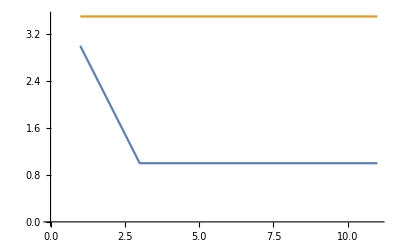

```mathematica
ListLinePlot[{definite2ArmBanditLearnList,Table[3.5,{x,definite2ArmBanditLearnList}] }] (* plot the learning curve of the automaton *)
```

Train a Tsetlin Automaton 10 times on an indefinite two-armed bandit problem.

```mathematica
indefinite2ArmBanditLearnList=NestList[ (* should learn 1, which usually (not always) wins here *)
TsetlinUpdate[
#,
3,
Position[
#,
TakeLargestBy[#,#&,1]⟦1⟧]⟦1⟧⟦1⟧&@{RandomVariate[NormalDistribution[0.75,.5]],RandomVariate[NormalDistribution[0.25,.5]]}]&,
4,10]
```

{4,3,2,1,1,1,1,1,1,1,1}

```mathematica
TsetlinAction[indefinite2ArmBanditLearnList[[-1]],3] (* outputs the final action choice of the automaton *)
```

1

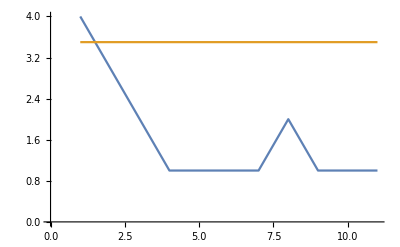

```mathematica
ListLinePlot[{indefinite2ArmBanditLearnList,Table[3.5,{x,indefinite2ArmBanditLearnList}] }](* plot the learning curve of the automaton *)
```

TsetlinWeightedReward rewards the Tsetlin Automaton depending on a probability based on s. This is important in a Tsetlin Machine.

```mathematica
TsetlinWeightedReward[t_Integer,si_Integer,s_?NumberQ]:=
If[
RandomReal[]≤((s-1)/s),
TsetlinReward[t,si],
t]
```

```mathematica
TsetlinWeightedReward[3,3,1]
```

3

```mathematica
TsetlinWeightedReward[3,3,1000]
```

2

TsetlinWeightedPunish is the punish equivalent of TsetlinWeightedReward.

```mathematica
TsetlinWeightedPunish[t_Integer,si_Integer,s_?NumberQ]:=
If[
RandomReal[]≤((s-1)/s),
TsetlinPunish[t,si],
t]
```

## Tsetlin Machine Basic Structure

Before the complete Tsetlin Machine head architecture is established, some heads important for building them need to be shown.

TsetlinClause[l, lneg] is a head that takes two arguments: the Tsetlin Automatons corresponding to the inputs as well as the ones corresponding to the negated inputs. TsetlinClauseNonNegated, when applied to a TsetlinClause, returns the list of automatons corresponding to the non-negated inputs. TsetlinClauseNegated returns the list of automatons corresponding to the negated inputs.

```mathematica
TsetlinClauseNonNegated[tc_TsetlinClause]:=tc[[1]]
```

```mathematica
TsetlinClauseNegated[tc_TsetlinClause]:=tc[[2]]
```

TsetlinOutput[l, f] is a head that takes two arguments: a list of conjunctive clauses and a function. It, when in use in a complete Tsetlin machine, reduces the outputs of each of the conjunctive clauses by applying the function, and returns the final output. TsetlinOutputClauses outputs the list of TsetlinClauses of a TsetlinOutput, and TsetlinOutputFunction returns the function.

```mathematica
TsetlinOutputClauses[to_TsetlinOutput]:=to[[1]]
```

```mathematica
TsetlinOutputFunction[to_TsetlinOutput]:=to[[2]]
```

TsetlinMachine[lc, si] is a head that represents a single-layer Tsetlin Machine. It takes two arguments: a list of TsetlinOutputs and the state identifier it uses for all of it’s automatons. Here is an example of a Tsetlin Machine that takes three inputs and produces two outputs (where each output has two clauses):

```mathematica
tm0=TsetlinMachine[
{
TsetlinOutput[
{
TsetlinClause[
{3,4,3},{4,4,3}],
TsetlinClause[
{3,3,3},{4,4,4}]
},
Or],
TsetlinOutput[
{
TsetlinClause[
{6,5,2},{3,2,4}],
TsetlinClause[
{2,3,2},{1,2,5}]
},
Or]
},
3]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,4,3},{4,4,3}],TsetlinClause[{3,3,3},{4,4,4}]},Or],TsetlinOutput[{TsetlinClause[{6,5,2},{3,2,4}],TsetlinClause[{2,3,2},{1,2,5}]},Or]},3]

TsetlinMachineOutputs takes a TsetlinMachine as input, and outputs the list of outputs,

```mathematica
TsetlinMachineOutputs[tm_TsetlinMachine]:=tm[[1]]
```

```mathematica
TsetlinMachineOutputs[tm0]
```

{TsetlinOutput[{TsetlinClause[{3,4,3},{4,4,3}],TsetlinClause[{3,3,3},{4,4,4}]},Or],TsetlinOutput[{TsetlinClause[{6,5,2},{3,2,4}],TsetlinClause[{2,3,2},{1,2,5}]},Or]}

TsetlinMachineStateIdentifier takes a TsetlinMachine as input, and outputs the StateIdentifier of the machine.

```mathematica
TsetlinMachineStateIdentifier[tm_TsetlinMachine]:=tm[[2]]
```

```mathematica
TsetlinMachineStateIdentifier[tm0]
```

3

Inputs in a Tsetlin machine are given in binary. Numerical input can be given, but the numbers need to be converted to binary (a list of boolean values). As such, a maximum and minimum value need to be established. Hopefully I can develop a system so that the programmer does not need to worry about this (e.g. handled automatically) but for now this has to be done manually.
An example list of inputs to a Tsetlin machine: {False,False,False,False,True,True,False,True} (representing integer 13).

ChangeBinaryForm is a helper function that converts a 1 or a 0 to a True or a False, and vice versa.

```mathematica
ChangeBinaryForm[t_]:=
If[
NumberQ@t,
t/.{0->False,1->True},
t/.{False->0,True->1}]
```

```mathematica
ChangeBinaryForm[1]
```

True

```mathematica
ChangeBinaryForm[False]
```

0

For the Tsetlin Automatons in the machine, 1 represents “exclude input” and 2 represents “include input”

TsetlinClauseSelectedInputs  takes a TsetlinClause, state identifier, and list of inputs. It returns a list of the inputs that the Tsetlin automaton of the clause have selected.

```mathematica
TsetlinClauseSelectedInputs[tc_TsetlinClause,si_Integer,li_List]:=
Last/@
Select[
Join[
Transpose[{
(TsetlinAction[#,si]&/@TsetlinClauseNonNegated[tc]),
li}],
Transpose[{
(TsetlinAction[#,si]&/@TsetlinClauseNegated[tc]),
Not/@li}]],
#[[1]]==2&]
```

```mathematica
TsetlinClauseSelectedInputs[ (* should output {True, True, False} *)
TsetlinClause[
{1,3,5},
{2,4,6}],
3,
{True, False, True}]
```

{True,True,False}

TsetlinClauseOutput takes a TsetlinClause, state identifier, and list of inputs as it’s arguments. It outputs either a 1 or 0, depending on the result of ANDing the selected inputs of the clause.

```mathematica
TsetlinClauseOutput[tc_TsetlinClause,si_Integer,li_List]:=
Fold[
And,
True,
TsetlinClauseSelectedInputs[tc,si,li]]
```

```mathematica
TsetlinClauseOutput[ (* should output False *)
TsetlinClause[
{1,3,5},
{2,4,6}],
3,
{True, False, True}]
```

False

TsetlinOutputResult takes a TsetlinOutput, state identifier, and list of inputs as it’s arguments. It returns the result of fold-applying the function of the TsetlinOutput to the TsetlinClause outputs calculated with the given state identifier and input.

```mathematica
TsetlinOutputResult[to_TsetlinOutput,si_Integer,li_List]:=
Fold[
TsetlinOutputFunction[to],
Map[
TsetlinClauseOutput[#,si,li]&,
TsetlinOutputClauses[to]]]
```

```mathematica
TsetlinOutputResult[ (* should output True *)
TsetlinOutput[
{TsetlinClause[
{1,3,5},
{2,4,6}],
TsetlinClause[
{6,1,6},
{1,1,2}]},
Or],
3,
{True, False, True}]
```

True

TsetlinMachineCalculateOutputs takes a TsetlinMachine and a list of inputs as input, and outputs a list of the outputs. This is the way to apply trained Tsetlin machines.

```mathematica
TsetlinMachineCalculateOutputs[tm_TsetlinMachine,li_List]:=
Map[
TsetlinOutputResult[
#,
TsetlinMachineStateIdentifier[tm],
li]&,
TsetlinMachineOutputs[tm]]
```

```mathematica
TsetlinMachineCalculateOutputs[ (* Should return {True, False} *)
TsetlinMachine[
{
TsetlinOutput[
{TsetlinClause[
{1,3,5},
{2,4,6}],
TsetlinClause[
{6,1,6},
{1,1,2}]},
Or],
TsetlinOutput[
{TsetlinClause[
{1,5,1},
{2,1,1}],
TsetlinClause[
{1,1,2},
{5,1,2}]},
Or]},
3],
{True, False, True}]
```

{True,False}

## Training a Tsetlin Machine

First, some functions for building the structure of Tsetlin machines (introduced from bottom up).

InitializeTsetlinAutomatonList takes 2 arguments: the state identifier and the length of the input.

```mathematica
InitializeTsetlinAutomatonList[si_Integer,il_Integer]:=
Table[RandomInteger[]+si,il]
```

```mathematica
InitializeTsetlinAutomatonList[3,3]
```

{3,3,4}

InitializeTsetlinClause takes 2 arguments: the state identifier and the length of the input.

```mathematica
InitializeTsetlinClause[si_Integer,il_Integer]:=
TsetlinClause[InitializeTsetlinAutomatonList[si,il],InitializeTsetlinAutomatonList[si,il]]
```

```mathematica
InitializeTsetlinClause[3,3]
```

TsetlinClause[{4,3,4},{4,3,4}]

InitializeTsetlinOutput takes 4 arguments: the state identifier, the length of the input, the number of clauses per the output, and the output function.

```mathematica
InitializeTsetlinOutput[si_Integer,il_Integer,nc_Integer, f_]:=
TsetlinOutput[
Table[
InitializeTsetlinClause[si,il],
nc],
f]
```

```mathematica
InitializeTsetlinOutput[3,3,2,Or]
```

TsetlinOutput[{TsetlinClause[{3,3,4},{4,3,4}],TsetlinClause[{4,4,4},{4,3,3}]},Or]

InitializeTsetlinMachine takes 4 arguments: the state identifier, the length of the input, the number of clauses per each output, and a list consisting of the output functions (the length of the list implicitly is equal to the number of outputs).

```mathematica
InitializeTsetlinMachine[si_Integer,il_Integer,nc_Integer,lf_List]:=
TsetlinMachine[
Map[
InitializeTsetlinOutput[
si,
il,
nc,
#]&,
lf],
si]
```

```mathematica
InitializeTsetlinMachine[3,3,2,{Or}]
(* Should produce something like:
TsetlinMachine[
{TsetlinOutput[
{
TsetlinClause[
{3,4,3},
{4,4,3}],
TsetlinClause[
{4,3,4},
{4,3,3}]},
Or]},
3]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,3,3},{4,3,4}],TsetlinClause[{3,4,3},{3,3,3}]},Or]},3]